```mathematica
(*算一下运动方程*)
(*上指标度规，下指标动量*)
ClearAll["Global`*"];
ClearAll[m];
m[r_]:=1-Qm^2/(2r)+(A Qm^4)/(40 r^5);
B=(7/4)A;
F01=-Qm((2a r Cos[θ])/(r^2+a^2 Cos[θ]^2)^2);
F02=-Qm(((r^2-a^2 Cos[θ]^2)a Sin[θ])/(r^2+a^2 Cos[θ]^2)^2);
Fdown={{0,F01,F02,0},{-F01,0,0,F01 a Sin[θ]^2},{-F02,0,0,((r^2+a^2)/a)F02},{0,-F01 a Sin[θ]^2,-((r^2+a^2)/a)F02,0}};
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 m[r]r+a^2;
gDown={{-(1-(2 m[r]r)/Σ),0,0,-(1/Σ)2 a m[r]r Sin[θ]^2},{0,Σ/Δ,0,0},{0,0,Σ,0},{-(1/Σ)2 a m[r]r Sin[θ]^2,0,0,(r^2+a^2+(1/Σ)2 m[r] a^2 r Sin[θ]^2)Sin[θ]^2}};
(*P形式的霍奇对偶*)
(*DualPup=-(1/(Σ Sin[θ])){{0,((r^2+a^2)/a)P02,-P01 a Sin[θ]^2,0},{-((r^2+a^2)/a)P02,0,0,-P02},{P01 a Sin[θ]^2,0,0,P01},{0,P02,-P01,0}};
DualPdown=gDown.DualPup.gDown//Simplify;
sp=(1/2)(P01^2-P02^2/(a^2 Sin[θ]^2));
tp=(-P01 P02)/(a Sin[θ]);*)
(*Fdown=(1-A sp)Pdown-B tp DualPdown//Simplify;*)
gij={{(-((a^2+r^2)^2-a^2 (a^2-2 m[r]r+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,-((2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)))},{0,(a^2-2 m[r]r+r^2)/(r^2+a^2 Cos[θ]^2),0,0},{0,0,1/(r^2+a^2 Cos[θ]^2),0},{-((2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2))),0,0,((a^2-2 m[r]r+r^2)-a^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)Sin[θ]^2)}};
Xdown=Fdown.gij.Fdown//Simplify;
(*Print[Xup[[2,3]]];
Print[Xup[[3,2]]];*)
QQ={-1,0,0,bb};
Gdown=gDown+k Xdown//Simplify;
Ginverse=Inverse[Gdown]//Simplify;
(*Print[Gdown[[2,3]]];
Print[Ginverse[[3,2]]];*)
H=(1/2)(Sum[Ginverse[[i,j]]QQ[[i]]QQ[[j]],{i,1,4},{j,1,4}])/.{θ->π/2}//Simplify;
HH=r^-2(k Qm^2-r^4) (A Qm^4-20 r^4 (a^2+Qm^2+(-2+r) r))H;
DHH=D[HH,r];
DDHH=D[DHH,r]
```

1/2 (20 r^4 (2 bb^2-12 r^2)-40 a bb (2 k Qm^2+12 (Qm^2-2 r) r^2-16 r^3)-a^2 (-80 k Qm^2-240 Qm^2 r^2+800 r^3+600 r^4)+160 r^3 (-4 r^3+bb^2 (-2+2 r))+240 r^2 (k Qm^2-r^4+bb^2 (Qm^2+(-2+r) r)))

```mathematica
CoefficientList[HH,bb]
```

{10 a^4 k Qm^2-1/2 a^2 A Qm^4+20 a^2 k Qm^2 r^2+10 a^2 Qm^2 r^4+10 k Qm^2 r^4-20 a^2 r^5-10 a^2 r^6-10 r^8,-20 a^3 k Qm^2+a A Qm^4-20 a (k Qm^2 r^2+(Qm^2-2 r) r^4),10 a^2 k Qm^2-(A Qm^4)/2+10 r^4 (Qm^2+(-2+r) r)}

```mathematica
a=1;
Qm=0;
A=0;
k=0;
{r,bb}/.FindRoot[{HH,DHH},{r,3},{bb,5}]
```

{1.,2.}

{0.1,0.4,30.4267}

{{0.,3.00579},{0.05,2.98618},{0.1,2.96587},{0.15,2.94478},{0.2,2.92286},{0.25,2.89999},{0.3,2.87609},{0.35,2.85103},{0.4,2.82465},{0.45,2.79677},{0.5,2.76716},{0.55,2.73553},{0.6,2.70149},{0.65,2.66453},{0.7,2.62394},{0.75,2.57865},{0.8,2.52701},{0.85,2.46617},{0.9,2.39031},{0.95,2.28365},{1.,1.91264}}

{{0.,1.91104},{0.05,1.91112},{0.1,1.9112},{0.15,1.91128},{0.2,1.91136},{0.25,1.91144},{0.3,1.91152},{0.35,1.9116},{0.4,1.91168},{0.45,1.91176},{0.5,1.91184},{0.55,1.91192},{0.6,1.912},{0.65,1.91208},{0.7,1.91216},{0.75,1.91224},{0.8,1.91232},{0.85,1.9124},{0.9,1.91248},{0.95,1.91256},{1.,1.91264}}

{{0.,1.57285},{0.05,1.56252},{0.1,1.55183},{0.15,1.54074},{0.2,1.5292},{0.25,1.51717},{0.3,1.50461},{0.35,1.49143},{0.4,1.47757},{0.45,1.46293},{0.5,1.44738},{0.55,1.43077},{0.6,1.41291},{0.65,1.39352},{0.7,1.37224},{0.75,1.3485},{0.8,1.32144},{0.85,1.28957},{0.9,1.24985},{0.95,1.19403},{1.,1.}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

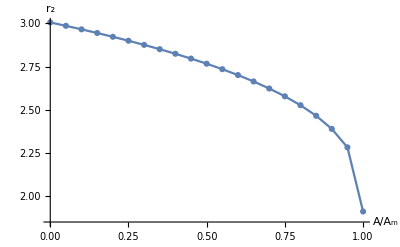

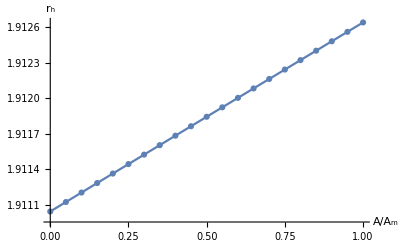

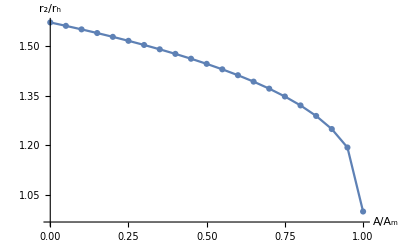

```mathematica
q={4,-7};
rr=Table[0,{i,1,21}];
n=Table[0,{i,1,21}];
sta=Table[0,{i,1,21}];
hori=Table[0,{i,1,21}];
{a,Qm}={0.1,0.4};
Am=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
Do[
A=0.05j Am;
k=0.875π   A;
horizon=Max[r/.NSolve[r^6-2m[r] r^5+r^4 a^2==0,r,Reals]];
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j+1]]={0.05j,re[[1]]};
n[[j+1]]={0.05j,re[[1]]/horizon};
sta[[j+1]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j+1]]={0.05j,horizon};
,{j,0,20}];
Print[{a,Qm,Am}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"A/A_m","r_2"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"A/A_m","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"A/A_m","r_2/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

{0.1,0.4,30.4267}

{{0.,2.76769},{0.05,2.74916},{0.1,2.73001},{0.15,2.71017},{0.2,2.68959},{0.25,2.66819},{0.3,2.64588},{0.35,2.62256},{0.4,2.5981},{0.45,2.57235},{0.5,2.54513},{0.55,2.5162},{0.6,2.48526},{0.65,2.4519},{0.7,2.41557},{0.75,2.37547},{0.8,2.33036},{0.85,2.27818},{0.9,2.21485},{0.95,2.12988},{1.,1.91264}}

{{0.,1.91104},{0.05,1.91112},{0.1,1.9112},{0.15,1.91128},{0.2,1.91136},{0.25,1.91144},{0.3,1.91152},{0.35,1.9116},{0.4,1.91168},{0.45,1.91176},{0.5,1.91184},{0.55,1.91192},{0.6,1.912},{0.65,1.91208},{0.7,1.91216},{0.75,1.91224},{0.8,1.91232},{0.85,1.9124},{0.9,1.91248},{0.95,1.91256},{1.,1.91264}}

{{0.,1.44826},{0.05,1.43851},{0.1,1.42842},{0.15,1.41799},{0.2,1.40716},{0.25,1.3959},{0.3,1.38417},{0.35,1.37191},{0.4,1.35906},{0.45,1.34554},{0.5,1.33124},{0.55,1.31606},{0.6,1.29982},{0.65,1.28232},{0.7,1.26327},{0.75,1.24224},{0.8,1.21861},{0.85,1.19127},{0.9,1.1581},{0.95,1.11363},{1.,1.}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

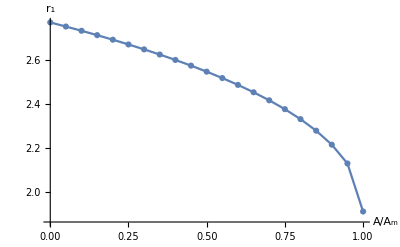

-Graphics-

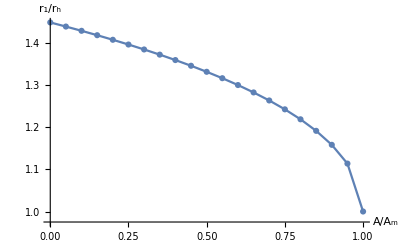

```mathematica
q={3,5};
rr=Table[0,{i,1,21}];
n=Table[0,{i,1,21}];
sta=Table[0,{i,1,21}];
hori=Table[0,{i,1,21}];
{a,Qm}={0.1,0.4};
Am=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
Do[
A=0.05j Am;
k=0.875π   A;
horizon=Max[r/.NSolve[r^6-2m[r] r^5+r^4 a^2==0,r,Reals]];
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j+1]]={0.05j,re[[1]]};
n[[j+1]]={0.05j,re[[1]]/horizon};
sta[[j+1]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j+1]]={0.05j,horizon};
,{j,0,20}];
Print[{a,Qm,Am}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"A/A_m","r_1"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"A/A_m","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"A/A_m","r_1/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

{{0.05,0.853216},{0.1,0.853882},{0.15,0.855002},{0.2,0.856591},{0.25,0.858671},{0.3,0.861274},{0.35,0.864438},{0.4,0.868217},{0.45,0.872678},{0.5,0.877908},{0.55,0.884023},{0.6,0.891178},{0.65,0.899588},{0.7,0.909573},{0.75,0.92164},{0.8,0.936759},{0.85,0.957787}}

{{0.05,1.86461},{0.1,1.86034},{0.15,1.85318},{0.2,1.84305},{0.25,1.82984},{0.3,1.81341},{0.35,1.79355},{0.4,1.77001},{0.45,1.74242},{0.5,1.71031},{0.55,1.67305},{0.6,1.62972},{0.65,1.57895},{0.7,1.51857},{0.75,1.44467},{0.8,1.34877},{0.85,1.2016}}

{{0.05,1.61555},{0.1,1.61846},{0.15,1.62338},{0.2,1.63043},{0.25,1.63977},{0.3,1.65163},{0.35,1.66633},{0.4,1.68431},{0.45,1.70616},{0.5,1.73271},{0.55,1.76517},{0.6,1.8053},{0.65,1.85591},{0.7,1.92175},{0.75,2.01193},{0.8,2.14783},{0.85,2.41027}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

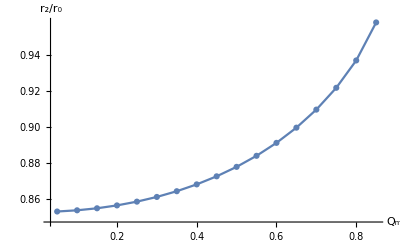

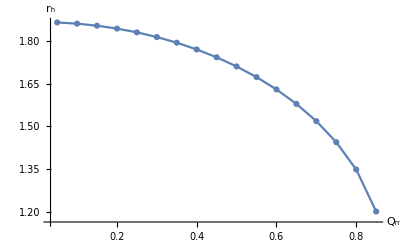

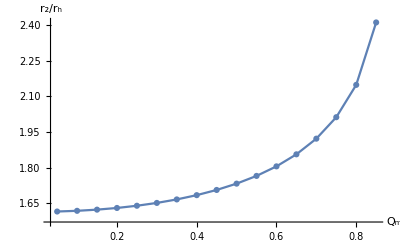

```mathematica
q={4,-7};
rr=Table[0,{i,1,17}];
n=Table[0,{i,1,17}];
sta=Table[0,{i,1,17}];
hori=Table[0,{i,1,17}];
a=0.5;
Do[
Qm=0.05j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π   A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j]]={Qm,re[[1]]/r0[[1]]};
n[[j]]={Qm,re[[1]]/horizon};
sta[[j]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j]]={Qm,horizon};
,{j,1,17}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"Q_m","r_2/r_0"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"Q_m","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"Q_m","r_2/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

{{0.05,0.795066},{0.1,0.795361},{0.15,0.795861},{0.2,0.796577},{0.25,0.79753},{0.3,0.798744},{0.35,0.800256},{0.4,0.802117},{0.45,0.804397},{0.5,0.807198},{0.55,0.81067},{0.6,0.815044},{0.65,0.820706},{0.7,0.828365},{0.75,0.839532},{0.8,0.85848},{0.85,0.911222}}

{{0.05,1.86461},{0.1,1.86034},{0.15,1.85318},{0.2,1.84305},{0.25,1.82984},{0.3,1.81341},{0.35,1.79355},{0.4,1.77001},{0.45,1.74242},{0.5,1.71031},{0.55,1.67305},{0.6,1.62972},{0.65,1.57895},{0.7,1.51857},{0.75,1.44467},{0.8,1.34877},{0.85,1.2016}}

{{0.05,1.},{0.1,1.},{0.15,1.},{0.2,1.},{0.25,1.},{0.3,1.},{0.35,1.},{0.4,1.},{0.45,1.},{0.5,1.},{0.55,1.},{0.6,1.},{0.65,1.},{0.7,1.},{0.75,1.},{0.8,1.},{0.85,1.}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

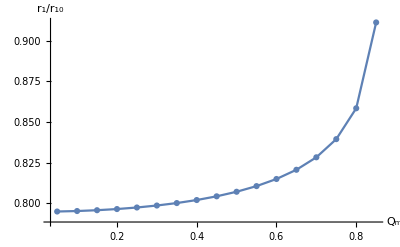

-Graphics-

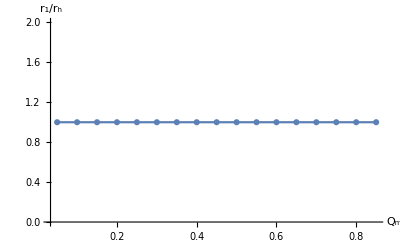

```mathematica
q={3,5};
rr=Table[0,{i,1,17}];
n=Table[0,{i,1,17}];
sta=Table[0,{i,1,17}];
hori=Table[0,{i,1,17}];
a=0.5;
Do[
Qm=0.05j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j]]={Qm,re[[1]]/r0[[1]]};
n[[j]]={Qm,re[[1]]/horizon};
sta[[j]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j]]={Qm,horizon};
,{j,1,17}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"Q_m","r_1/r_10"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"Q_m","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"Q_m","r_1/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

{{0.,0.663876},{0.03,0.655661},{0.06,0.647405},{0.09,0.6391},{0.12,0.646052},{0.15,0.674141},{0.18,0.698977},{0.21,0.721309},{0.24,0.741637},{0.27,0.760311},{0.3,0.777591},{0.33,0.793674},{0.36,0.808715},{0.39,0.822837},{0.42,0.836142},{0.45,0.848712},{0.48,0.860619},{0.51,0.871921},{0.54,0.882671},{0.57,0.892913},{0.6,0.902687}}

{{0.,1.9181},{0.03,1.91761},{0.06,1.91614},{0.09,1.91368},{0.12,1.91023},{0.15,1.90577},{0.18,1.90028},{0.21,1.89376},{0.24,1.88618},{0.27,1.8775},{0.3,1.8677},{0.33,1.85674},{0.36,1.84458},{0.39,1.83115},{0.42,1.8164},{0.45,1.80026},{0.48,1.78263},{0.51,1.76342},{0.54,1.7425},{0.57,1.71973},{0.6,1.69492}}

{{0.,1.},{0.03,1.},{0.06,1.},{0.09,1.},{0.12,1.02428},{0.15,1.08329},{0.18,1.13875},{0.21,1.1918},{0.24,1.24321},{0.27,1.29356},{0.3,1.34329},{0.33,1.39279},{0.36,1.44239},{0.39,1.49241},{0.42,1.54314},{0.45,1.59489},{0.48,1.64799},{0.51,1.70278},{0.54,1.75968},{0.57,1.81915},{0.6,1.88174}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

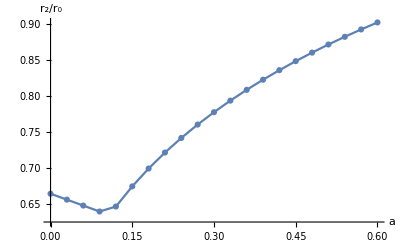

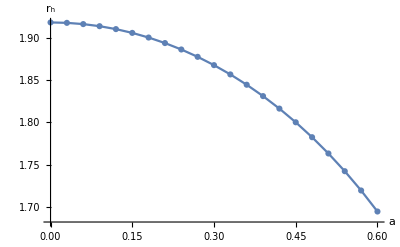

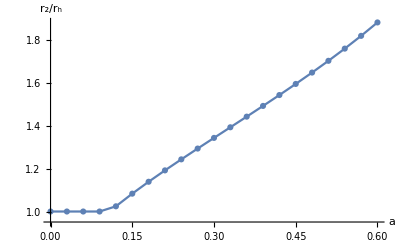

```mathematica
q={4,-7};
rr=Table[0,{i,1,21}];
n=Table[0,{i,1,21}];
sta=Table[0,{i,1,21}];
hori=Table[0,{i,1,21}];
Qm=0.4;
Do[
a=0.03j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π   A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j+1]]={a,re[[1]]/r0[[1]]};
n[[j+1]]={a,re[[1]]/horizon};
sta[[j+1]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j+1]]={a,horizon};
,{j,0,20}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"a","r_2/r_0"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"a","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"a","r_2/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

{{0.,0.666511},{0.03,0.674221},{0.06,0.681904},{0.09,0.689566},{0.12,0.697211},{0.15,0.704846},{0.18,0.712476},{0.21,0.720108},{0.24,0.727748},{0.27,0.735402},{0.3,0.743076},{0.33,0.750779},{0.36,0.758517},{0.39,0.766299},{0.42,0.774134},{0.45,0.78203},{0.48,0.790001},{0.51,0.798056},{0.54,0.806212},{0.57,0.814482},{0.6,0.822886}}

{{0.,1.99508},{0.03,1.99463},{0.06,1.99327},{0.09,1.991},{0.12,1.98782},{0.15,1.98371},{0.18,1.97866},{0.21,1.97267},{0.24,1.9657},{0.27,1.95775},{0.3,1.94878},{0.33,1.93877},{0.36,1.92768},{0.39,1.91547},{0.42,1.9021},{0.45,1.88751},{0.48,1.87165},{0.51,1.85445},{0.54,1.83581},{0.57,1.81565},{0.6,1.79384}}

{{0.,1.},{0.03,1.},{0.06,1.},{0.09,1.},{0.12,1.},{0.15,1.},{0.18,1.},{0.21,1.},{0.24,1.},{0.27,1.},{0.3,1.},{0.33,1.},{0.36,1.},{0.39,1.},{0.42,1.},{0.45,1.},{0.48,1.},{0.51,1.},{0.54,1.},{0.57,1.},{0.6,1.}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

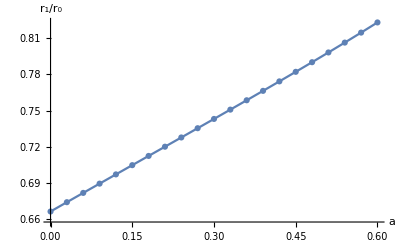

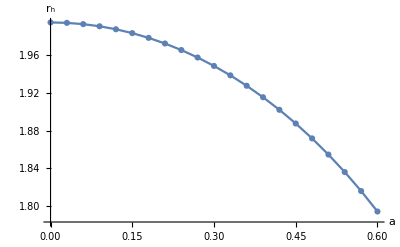

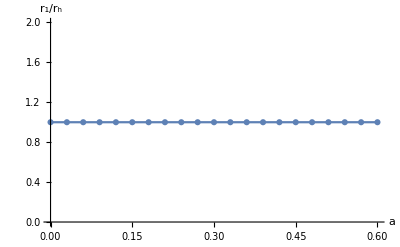

```mathematica
q={3,5};
rr=Table[0,{i,1,21}];
n=Table[0,{i,1,21}];
sta=Table[0,{i,1,21}];
hori=Table[0,{i,1,21}];
Qm=0.1;
Do[
a=0.03j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π  A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[j+1]]={a,re[[1]]/r0[[1]]};
n[[j+1]]={a,re[[1]]/horizon};
sta[[j+1]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[j+1]]={a,horizon};
,{j,0,20}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListLinePlot[rr,AxesLabel->{"a","r_1/r_0"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[hori,AxesLabel->{"a","r_h"},PlotRange->All,PlotMarkers->Automatic]
ListLinePlot[n,AxesLabel->{"a","r_1/r_h"},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
q={4,-7};
rr=Table[0,{i,1,336}];
n=Table[0,{i,1,336}];
sta=Table[0,{i,1,336}];
hori=Table[0,{i,1,336}];
Do[
a=0.03i;
Do[
Qm=0.05j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π   A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[16i+j]]={a,Qm,re[[1]]/r0[[1]]};
n[[16i+j]]={a,Qm,re[[1]]/horizon};
sta[[16i+j]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[16i+j]]={a,Qm,horizon};
,{j,1,16}];
,{i,0,20}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListPlot3D[rr,AxesLabel->{"a","Q_m","r_2/r_0"},PlotRange->All]
ListPlot3D[hori,AxesLabel->{"a","Q_m","r_h"},PlotRange->All]
ListPlot3D[n,AxesLabel->{"a","Q_m","r_2/r_h"},PlotRange->All]
```

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，FindRoot::cvmit 的进一步输出将被抑制.

{{0.,0.05,0.666628},{0.,0.1,0.666511},{0.,0.15,0.666313},{0.,0.2,0.66603},{0.,0.25,0.665655},{0.,0.3,0.66518},{0.,0.35,0.664592},{0.,0.4,0.663876},{0.,0.45,0.663011},{0.,0.5,0.661966},{0.,0.55,0.660702},{0.,0.6,0.659162},{0.,0.65,0.657266},{0.,0.7,0.654889},{0.,0.75,0.651835},{0.,0.8,0.647766},{0.03,0.05,0.658905},{0.03,0.1,0.658767},{0.03,0.15,0.658533},{0.03,0.2,0.658198},{0.03,0.25,0.657756},{0.03,0.3,0.657196},{0.03,0.35,0.656504},{0.03,0.4,0.655661},{0.03,0.45,0.654644},{0.03,0.5,0.653417},{0.03,0.55,0.651937},{0.03,0.6,0.650139},{0.03,0.65,0.647929},{0.03,0.7,0.64517},{0.03,0.75,0.64164},{0.03,0.8,0.636964},{0.06,0.05,0.651143},{0.06,0.1,0.650983},{0.06,0.15,0.650713},{0.06,0.2,0.650328},{0.06,0.25,0.649818},{0.06,0.3,0.649172},{0.06,0.35,0.648375},{0.06,0.4,0.647405},{0.06,0.45,0.646235},{0.06,0.5,0.644827},{0.06,0.55,0.64313},{0.06,0.6,0.641072},{0.06,0.65,0.638549},{0.06,0.7,0.635406},{0.06,0.75,0.631964},{0.06,0.8,0.650809},{0.09,0.05,0.643336},{0.09,0.1,0.643155},{0.09,0.15,0.642848},{0.09,0.2,0.642411},{0.09,0.25,0.641833},{0.09,0.3,0.641101},{0.09,0.35,0.640198},{0.09,0.4,0.6391},{0.09,0.45,0.637776},{0.09,0.5,0.636185},{0.09,0.55,0.63427},{0.09,0.6,0.636903},{0.09,0.65,0.64611},{0.09,0.7,0.657435},{0.09,0.75,0.671589},{0.09,0.8,0.689685},{0.12,0.05,0.635478},{0.12,0.1,0.635274},{0.12,0.15,0.634944},{0.12,0.2,0.634394},{0.12,0.25,0.636763},{0.12,0.3,0.63926},{0.12,0.35,0.642332},{0.12,0.4,0.646052},{0.12,0.45,0.650516},{0.12,0.5,0.655848},{0.12,0.55,0.662216},{0.12,0.6,0.669843},{0.12,0.65,0.679041},{0.12,0.7,0.69025},{0.12,0.75,0.704118},{0.12,0.8,0.721652},{0.15,0.05,0.659365},{0.15,0.1,0.660005},{0.15,0.15,0.661086},{0.15,0.2,0.662626},{0.15,0.25,0.664655},{0.15,0.3,0.667212},{0.15,0.35,0.670351},{0.15,0.4,0.674141},{0.15,0.45,0.678672},{0.15,0.5,0.684065},{0.15,0.55,0.690476},{0.15,0.6,0.698117},{0.15,0.65,0.707278},{0.15,0.7,0.71837},{0.15,0.75,0.731995},{0.15,0.8,0.749081},{0.18,0.05,0.683983},{0.18,0.1,0.684636},{0.18,0.15,0.685737},{0.18,0.2,0.687305},{0.18,0.25,0.689367},{0.18,0.3,0.691963},{0.18,0.35,0.695144},{0.18,0.4,0.698977},{0.18,0.45,0.703548},{0.18,0.5,0.708972},{0.18,0.55,0.715399},{0.18,0.6,0.72303},{0.18,0.65,0.73214},{0.18,0.7,0.743115},{0.18,0.75,0.756522},{0.18,0.8,0.773231},{0.21,0.05,0.706176},{0.21,0.1,0.706837},{0.21,0.15,0.707952},{0.21,0.2,0.709538},{0.21,0.25,0.711623},{0.21,0.3,0.714244},{0.21,0.35,0.717451},{0.21,0.4,0.721309},{0.21,0.45,0.725902},{0.21,0.5,0.731339},{0.21,0.55,0.737765},{0.21,0.6,0.745371},{0.21,0.65,0.75442},{0.21,0.7,0.765281},{0.21,0.75,0.778489},{0.21,0.8,0.794869},{0.24,0.05,0.726416},{0.24,0.1,0.727084},{0.24,0.15,0.728207},{0.24,0.2,0.729805},{0.24,0.25,0.731905},{0.24,0.3,0.734542},{0.24,0.35,0.737765},{0.24,0.4,0.741637},{0.24,0.45,0.746238},{0.24,0.5,0.751676},{0.24,0.55,0.758088},{0.24,0.6,0.76566},{0.24,0.65,0.774644},{0.24,0.7,0.785391},{0.24,0.75,0.798415},{0.24,0.8,0.814504},{0.27,0.05,0.745043},{0.27,0.1,0.745713},{0.27,0.15,0.746843},{0.27,0.2,0.748449},{0.27,0.25,0.750557},{0.27,0.3,0.753203},{0.27,0.35,0.756434},{0.27,0.4,0.760311},{0.27,0.45,0.764912},{0.27,0.5,0.770341},{0.27,0.55,0.776732},{0.27,0.6,0.784263},{0.27,0.65,0.793177},{0.27,0.7,0.803814},{0.27,0.75,0.816667},{0.27,0.8,0.832497},{0.3,0.05,0.762304},{0.3,0.1,0.762977},{0.3,0.15,0.76411},{0.3,0.2,0.76572},{0.3,0.25,0.767833},{0.3,0.3,0.770483},{0.3,0.35,0.773716},{0.3,0.4,0.777591},{0.3,0.45,0.782185},{0.3,0.5,0.787599},{0.3,0.55,0.793962},{0.3,0.6,0.801448},{0.3,0.65,0.81029},{0.3,0.7,0.820819},{0.3,0.75,0.833513},{0.3,0.8,0.849113},{0.33,0.05,0.778391},{0.33,0.1,0.779066},{0.33,0.15,0.7802},{0.33,0.2,0.781811},{0.33,0.25,0.783925},{0.33,0.3,0.786575},{0.33,0.35,0.789805},{0.33,0.4,0.793674},{0.33,0.45,0.798257},{0.33,0.5,0.80365},{0.33,0.55,0.809981},{0.33,0.6,0.817417},{0.33,0.65,0.826188},{0.33,0.7,0.836614},{0.33,0.75,0.849161},{0.33,0.8,0.864559},{0.36,0.05,0.793455},{0.36,0.1,0.794129},{0.36,0.15,0.795263},{0.36,0.2,0.796874},{0.36,0.25,0.798986},{0.36,0.3,0.801632},{0.36,0.35,0.804856},{0.36,0.4,0.808715},{0.36,0.45,0.813281},{0.36,0.5,0.81865},{0.36,0.55,0.824946},{0.36,0.6,0.832332},{0.36,0.65,0.841031},{0.36,0.7,0.851358},{0.36,0.75,0.863772},{0.36,0.8,0.879},{0.39,0.05,0.807614},{0.39,0.1,0.808288},{0.39,0.15,0.809421},{0.39,0.2,0.811029},{0.39,0.25,0.813137},{0.39,0.3,0.815777},{0.39,0.35,0.818992},{0.39,0.4,0.822837},{0.39,0.45,0.827384},{0.39,0.5,0.832726},{0.39,0.55,0.838984},{0.39,0.6,0.846318},{0.39,0.65,0.854948},{0.39,0.7,0.865183},{0.39,0.75,0.877479},{0.39,0.8,0.892572},{0.42,0.05,0.820968},{0.42,0.1,0.82164},{0.42,0.15,0.82277},{0.42,0.2,0.824375},{0.42,0.25,0.826477},{0.42,0.3,0.829109},{0.42,0.35,0.832312},{0.42,0.4,0.836142},{0.42,0.45,0.840667},{0.42,0.5,0.84598},{0.42,0.55,0.852199},{0.42,0.6,0.859481},{0.42,0.65,0.868045},{0.42,0.7,0.878195},{0.42,0.75,0.890391},{0.42,0.8,0.905392},{0.45,0.05,0.833597},{0.45,0.1,0.834267},{0.45,0.15,0.835394},{0.45,0.2,0.836994},{0.45,0.25,0.839089},{0.45,0.3,0.841711},{0.45,0.35,0.844901},{0.45,0.4,0.848712},{0.45,0.45,0.853214},{0.45,0.5,0.858496},{0.45,0.55,0.864675},{0.45,0.6,0.871908},{0.45,0.65,0.880409},{0.45,0.7,0.890484},{0.45,0.75,0.902605},{0.45,0.8,0.917572},{0.48,0.05,0.84557},{0.48,0.1,0.846237},{0.48,0.15,0.84736},{0.48,0.2,0.848954},{0.48,0.25,0.851041},{0.48,0.3,0.853651},{0.48,0.35,0.856826},{0.48,0.4,0.860619},{0.48,0.45,0.865096},{0.48,0.5,0.870347},{0.48,0.55,0.876487},{0.48,0.6,0.883672},{0.48,0.65,0.892116},{0.48,0.7,0.902131},{0.48,0.75,0.914205},{0.48,0.8,0.929223},{0.51,0.05,0.856944},{0.51,0.1,0.857609},{0.51,0.15,0.858727},{0.51,0.2,0.860314},{0.51,0.25,0.862391},{0.51,0.3,0.86499},{0.51,0.35,0.868149},{0.51,0.4,0.871921},{0.51,0.45,0.876373},{0.51,0.5,0.881593},{0.51,0.55,0.887695},{0.51,0.6,0.894836},{0.51,0.65,0.903232},{0.51,0.7,0.913205},{0.51,0.75,0.925277},{0.51,0.8,0.940476},{0.54,0.05,0.867769},{0.54,0.1,0.868431},{0.54,0.15,0.869545},{0.54,0.2,0.871124},{0.54,0.25,0.873191},{0.54,0.3,0.875776},{0.54,0.35,0.878919},{0.54,0.4,0.882671},{0.54,0.45,0.887098},{0.54,0.5,0.892287},{0.54,0.55,0.898355},{0.54,0.6,0.905457},{0.54,0.65,0.913817},{0.54,0.7,0.923773},{0.54,0.75,0.935909},{0.54,0.8,0.951523},{0.57,0.05,0.878089},{0.57,0.1,0.878748},{0.57,0.15,0.879856},{0.57,0.2,0.881427},{0.57,0.25,0.883484},{0.57,0.3,0.886056},{0.57,0.35,0.889182},{0.57,0.4,0.892913},{0.57,0.45,0.897315},{0.57,0.5,0.902477},{0.57,0.55,0.908513},{0.57,0.6,0.915585},{0.57,0.65,0.923926},{0.57,0.7,0.933905},{0.57,0.75,0.94621},{0.57,0.8,0.962758},{0.6,0.05,0.887942},{0.6,0.1,0.888597},{0.6,0.15,0.8897},{0.6,0.2,0.891263},{0.6,0.25,0.893309},{0.6,0.3,0.895867},{0.6,0.35,0.898976},{0.6,0.4,0.902687},{0.6,0.45,0.907067},{0.6,0.5,0.912203},{0.6,0.55,0.918215},{0.6,0.6,0.92527},{0.6,0.65,0.933617},{0.6,0.7,0.943679},{0.6,0.75,0.956349},{0.6,0.8,0.975754}}

{{0.,0.05,1.99877},{0.,0.1,1.99508},{0.,0.15,1.98889},{0.,0.2,1.98017},{0.,0.25,1.96883},{0.,0.3,1.9548},{0.,0.35,1.93794},{0.,0.4,1.9181},{0.,0.45,1.89509},{0.,0.5,1.86865},{0.,0.55,1.83845},{0.,0.6,1.80408},{0.,0.65,1.76497},{0.,0.7,1.72036},{0.,0.75,1.66913},{0.,0.8,1.60962},{0.03,0.05,1.99832},{0.03,0.1,1.99463},{0.03,0.15,1.98844},{0.03,0.2,1.97971},{0.03,0.25,1.96837},{0.03,0.3,1.95433},{0.03,0.35,1.93746},{0.03,0.4,1.91761},{0.03,0.45,1.89459},{0.03,0.5,1.86813},{0.03,0.55,1.83792},{0.03,0.6,1.80352},{0.03,0.65,1.76439},{0.03,0.7,1.71973},{0.03,0.75,1.66845},{0.03,0.8,1.60889},{0.06,0.05,1.99697},{0.06,0.1,1.99327},{0.06,0.15,1.98707},{0.06,0.2,1.97833},{0.06,0.25,1.96697},{0.06,0.3,1.95291},{0.06,0.35,1.93602},{0.06,0.4,1.91614},{0.06,0.45,1.89308},{0.06,0.5,1.86657},{0.06,0.55,1.8363},{0.06,0.6,1.80184},{0.06,0.65,1.76262},{0.06,0.7,1.71785},{0.06,0.75,1.66643},{0.06,0.8,1.60666},{0.09,0.05,1.99471},{0.09,0.1,1.991},{0.09,0.15,1.98479},{0.09,0.2,1.97603},{0.09,0.25,1.96464},{0.09,0.3,1.95055},{0.09,0.35,1.93361},{0.09,0.4,1.91368},{0.09,0.45,1.89055},{0.09,0.5,1.86397},{0.09,0.55,1.83361},{0.09,0.6,1.79903},{0.09,0.65,1.75966},{0.09,0.7,1.71471},{0.09,0.75,1.66305},{0.09,0.8,1.60294},{0.12,0.05,1.99154},{0.12,0.1,1.98782},{0.12,0.15,1.98159},{0.12,0.2,1.97279},{0.12,0.25,1.96137},{0.12,0.3,1.94723},{0.12,0.35,1.93023},{0.12,0.4,1.91023},{0.12,0.45,1.88701},{0.12,0.5,1.86032},{0.12,0.55,1.82982},{0.12,0.6,1.79508},{0.12,0.65,1.7555},{0.12,0.7,1.71029},{0.12,0.75,1.65828},{0.12,0.8,1.5977},{0.15,0.05,1.98744},{0.15,0.1,1.98371},{0.15,0.15,1.97745},{0.15,0.2,1.96862},{0.15,0.25,1.95715},{0.15,0.3,1.94294},{0.15,0.35,1.92587},{0.15,0.4,1.90577},{0.15,0.45,1.88243},{0.15,0.5,1.8556},{0.15,0.55,1.82493},{0.15,0.6,1.78997},{0.15,0.65,1.75012},{0.15,0.7,1.70457},{0.15,0.75,1.6521},{0.15,0.8,1.59088},{0.18,0.05,1.98242},{0.18,0.1,1.97866},{0.18,0.15,1.97237},{0.18,0.2,1.9635},{0.18,0.25,1.95196},{0.18,0.3,1.93768},{0.18,0.35,1.9205},{0.18,0.4,1.90028},{0.18,0.45,1.8768},{0.18,0.5,1.84979},{0.18,0.55,1.8189},{0.18,0.6,1.78368},{0.18,0.65,1.7435},{0.18,0.7,1.6975},{0.18,0.75,1.64446},{0.18,0.8,1.58244},{0.21,0.05,1.97645},{0.21,0.1,1.97267},{0.21,0.15,1.96634},{0.21,0.2,1.95741},{0.21,0.25,1.9458},{0.21,0.3,1.93142},{0.21,0.35,1.91413},{0.21,0.4,1.89376},{0.21,0.45,1.87011},{0.21,0.5,1.84288},{0.21,0.55,1.81173},{0.21,0.6,1.77618},{0.21,0.65,1.73558},{0.21,0.7,1.68907},{0.21,0.75,1.63532},{0.21,0.8,1.57231},{0.24,0.05,1.96951},{0.24,0.1,1.9657},{0.24,0.15,1.95933},{0.24,0.2,1.95033},{0.24,0.25,1.93864},{0.24,0.3,1.92414},{0.24,0.35,1.90671},{0.24,0.4,1.88618},{0.24,0.45,1.86231},{0.24,0.5,1.83483},{0.24,0.55,1.80337},{0.24,0.6,1.76743},{0.24,0.65,1.72635},{0.24,0.7,1.6792},{0.24,0.75,1.6246},{0.24,0.8,1.56039},{0.27,0.05,1.96158},{0.27,0.1,1.95775},{0.27,0.15,1.95132},{0.27,0.2,1.94225},{0.27,0.25,1.93045},{0.27,0.3,1.91583},{0.27,0.35,1.89824},{0.27,0.4,1.8775},{0.27,0.45,1.8534},{0.27,0.5,1.82562},{0.27,0.55,1.79379},{0.27,0.6,1.7574},{0.27,0.65,1.71574},{0.27,0.7,1.66784},{0.27,0.75,1.61223},{0.27,0.8,1.54657},{0.3,0.05,1.95265},{0.3,0.1,1.94878},{0.3,0.15,1.94229},{0.3,0.2,1.93313},{0.3,0.25,1.92121},{0.3,0.3,1.90644},{0.3,0.35,1.88867},{0.3,0.4,1.8677},{0.3,0.45,1.84332},{0.3,0.5,1.8152},{0.3,0.55,1.78294},{0.3,0.6,1.74602},{0.3,0.65,1.70369},{0.3,0.7,1.65491},{0.3,0.75,1.59811},{0.3,0.8,1.5307},{0.33,0.05,1.94268},{0.33,0.1,1.93877},{0.33,0.15,1.93221},{0.33,0.2,1.92295},{0.33,0.25,1.9109},{0.33,0.3,1.89596},{0.33,0.35,1.87797},{0.33,0.4,1.85674},{0.33,0.45,1.83204},{0.33,0.5,1.80352},{0.33,0.55,1.77078},{0.33,0.6,1.73324},{0.33,0.65,1.69013},{0.33,0.7,1.64032},{0.33,0.75,1.58209},{0.33,0.8,1.51258},{0.36,0.05,1.93164},{0.36,0.1,1.92768},{0.36,0.15,1.92104},{0.36,0.2,1.91166},{0.36,0.25,1.89946},{0.36,0.3,1.88433},{0.36,0.35,1.8661},{0.36,0.4,1.84458},{0.36,0.45,1.8195},{0.36,0.5,1.79054},{0.36,0.55,1.75723},{0.36,0.6,1.71899},{0.36,0.65,1.67497},{0.36,0.7,1.62395},{0.36,0.75,1.56403},{0.36,0.8,1.49198},{0.39,0.05,1.91948},{0.39,0.1,1.91547},{0.39,0.15,1.90874},{0.39,0.2,1.89924},{0.39,0.25,1.88687},{0.39,0.3,1.87151},{0.39,0.35,1.85301},{0.39,0.4,1.83115},{0.39,0.45,1.80566},{0.39,0.5,1.77617},{0.39,0.55,1.74223},{0.39,0.6,1.70317},{0.39,0.65,1.65809},{0.39,0.7,1.60565},{0.39,0.75,1.54372},{0.39,0.8,1.46855},{0.42,0.05,1.90617},{0.42,0.1,1.9021},{0.42,0.15,1.89527},{0.42,0.2,1.88562},{0.42,0.25,1.87306},{0.42,0.3,1.85746},{0.42,0.35,1.83865},{0.42,0.4,1.8164},{0.42,0.45,1.79043},{0.42,0.5,1.76036},{0.42,0.55,1.72567},{0.42,0.6,1.68567},{0.42,0.65,1.63936},{0.42,0.7,1.58525},{0.42,0.75,1.52089},{0.42,0.8,1.44186},{0.45,0.05,1.89165},{0.45,0.1,1.88751},{0.45,0.15,1.88057},{0.45,0.2,1.87076},{0.45,0.25,1.85798},{0.45,0.3,1.8421},{0.45,0.35,1.82294},{0.45,0.4,1.80026},{0.45,0.45,1.77375},{0.45,0.5,1.743},{0.45,0.55,1.70746},{0.45,0.6,1.66637},{0.45,0.65,1.61862},{0.45,0.7,1.56251},{0.45,0.75,1.49521},{0.45,0.8,1.41127},{0.48,0.05,1.87587},{0.48,0.1,1.87165},{0.48,0.15,1.86459},{0.48,0.2,1.85459},{0.48,0.25,1.84157},{0.48,0.3,1.82537},{0.48,0.35,1.80581},{0.48,0.4,1.78263},{0.48,0.45,1.7555},{0.48,0.5,1.72398},{0.48,0.55,1.68746},{0.48,0.6,1.6451},{0.48,0.65,1.59564},{0.48,0.7,1.53713},{0.48,0.75,1.46619},{0.48,0.8,1.37582},{0.51,0.05,1.85875},{0.51,0.1,1.85445},{0.51,0.15,1.84724},{0.51,0.2,1.83703},{0.51,0.25,1.82373},{0.51,0.3,1.80718},{0.51,0.35,1.78716},{0.51,0.4,1.76342},{0.51,0.45,1.73558},{0.51,0.5,1.70317},{0.51,0.55,1.66551},{0.51,0.6,1.62165},{0.51,0.65,1.57016},{0.51,0.7,1.50874},{0.51,0.75,1.43316},{0.51,0.8,1.33398},{0.54,0.05,1.84021},{0.54,0.1,1.83581},{0.54,0.15,1.82844},{0.54,0.2,1.818},{0.54,0.25,1.80439},{0.54,0.3,1.78742},{0.54,0.35,1.7669},{0.54,0.4,1.7425},{0.54,0.45,1.71385},{0.54,0.5,1.6804},{0.54,0.55,1.64141},{0.54,0.6,1.59578},{0.54,0.65,1.54183},{0.54,0.7,1.47677},{0.54,0.75,1.39513},{0.54,0.8,1.28292},{0.57,0.05,1.82015},{0.57,0.1,1.81565},{0.57,0.15,1.80809},{0.57,0.2,1.79739},{0.57,0.25,1.78341},{0.57,0.3,1.76599},{0.57,0.35,1.74487},{0.57,0.4,1.71973},{0.57,0.45,1.69013},{0.57,0.5,1.65547},{0.57,0.55,1.6149},{0.57,0.6,1.56714},{0.57,0.65,1.51018},{0.57,0.7,1.44047},{0.57,0.75,1.35047},{0.57,0.8,1.2162},{0.6,0.05,1.79846},{0.6,0.1,1.79384},{0.6,0.15,1.78607},{0.6,0.2,1.77507},{0.6,0.25,1.76068},{0.6,0.3,1.74272},{0.6,0.35,1.72092},{0.6,0.4,1.69492},{0.6,0.45,1.66422},{0.6,0.5,1.62813},{0.6,0.55,1.58566},{0.6,0.6,1.5353},{0.6,0.65,1.47454},{0.6,0.7,1.39864},{0.6,0.75,1.29619},{0.6,0.8,1.10789}}

{{0.,0.05,1.},{0.,0.1,1.},{0.,0.15,1.},{0.,0.2,1.},{0.,0.25,1.},{0.,0.3,1.},{0.,0.35,1.},{0.,0.4,1.},{0.,0.45,1.},{0.,0.5,1.},{0.,0.55,1.},{0.,0.6,1.},{0.,0.65,1.},{0.,0.7,1.},{0.,0.75,1.},{0.,0.8,1.},{0.03,0.05,1.},{0.03,0.1,1.},{0.03,0.15,1.},{0.03,0.2,1.},{0.03,0.25,1.},{0.03,0.3,1.},{0.03,0.35,1.},{0.03,0.4,1.},{0.03,0.45,1.},{0.03,0.5,1.},{0.03,0.55,1.},{0.03,0.6,1.},{0.03,0.65,1.},{0.03,0.7,1.},{0.03,0.75,1.},{0.03,0.8,1.},{0.06,0.05,1.},{0.06,0.1,1.},{0.06,0.15,1.},{0.06,0.2,1.},{0.06,0.25,1.},{0.06,0.3,1.},{0.06,0.35,1.},{0.06,0.4,1.},{0.06,0.45,1.},{0.06,0.5,1.},{0.06,0.55,1.},{0.06,0.6,1.},{0.06,0.65,1.},{0.06,0.7,1.},{0.06,0.75,1.00089},{0.06,0.8,1.03944},{0.09,0.05,1.},{0.09,0.1,1.},{0.09,0.15,1.},{0.09,0.2,1.},{0.09,0.25,1.},{0.09,0.3,1.},{0.09,0.35,1.},{0.09,0.4,1.},{0.09,0.45,1.},{0.09,0.5,1.},{0.09,0.55,1.},{0.09,0.6,1.00784},{0.09,0.65,1.02702},{0.09,0.7,1.05092},{0.09,0.75,1.0813},{0.09,0.8,1.12109},{0.12,0.05,1.},{0.12,0.1,1.},{0.12,0.15,1.00002},{0.12,0.2,0.999925},{0.12,0.25,1.00468},{0.12,0.3,1.00993},{0.12,0.35,1.0164},{0.12,0.4,1.02428},{0.12,0.45,1.03378},{0.12,0.5,1.0452},{0.12,0.55,1.05896},{0.12,0.6,1.0756},{0.12,0.65,1.09593},{0.12,0.7,1.12112},{0.12,0.75,1.15297},{0.12,0.8,1.19446},{0.15,0.05,1.05068},{0.15,0.1,1.05208},{0.15,0.15,1.05444},{0.15,0.2,1.05781},{0.15,0.25,1.06227},{0.15,0.3,1.0679},{0.15,0.35,1.07485},{0.15,0.4,1.08329},{0.15,0.45,1.09344},{0.15,0.5,1.10563},{0.15,0.55,1.12027},{0.15,0.6,1.13794},{0.15,0.65,1.15946},{0.15,0.7,1.18605},{0.15,0.75,1.21959},{0.15,0.8,1.26317},{0.18,0.05,1.10395},{0.18,0.1,1.10544},{0.18,0.15,1.10797},{0.18,0.2,1.11157},{0.18,0.25,1.11633},{0.18,0.3,1.12235},{0.18,0.35,1.12976},{0.18,0.4,1.13875},{0.18,0.45,1.14956},{0.18,0.5,1.16252},{0.18,0.55,1.17807},{0.18,0.6,1.19681},{0.18,0.65,1.2196},{0.18,0.7,1.24773},{0.18,0.75,1.28318},{0.18,0.8,1.32925},{0.21,0.05,1.15477},{0.21,0.1,1.15637},{0.21,0.15,1.15906},{0.21,0.2,1.1629},{0.21,0.25,1.16796},{0.21,0.3,1.17436},{0.21,0.35,1.18224},{0.21,0.4,1.1918},{0.21,0.45,1.20329},{0.21,0.5,1.21705},{0.21,0.55,1.23355},{0.21,0.6,1.25343},{0.21,0.65,1.2776},{0.21,0.7,1.30744},{0.21,0.75,1.34505},{0.21,0.8,1.394},{0.24,0.05,1.20388},{0.24,0.1,1.20558},{0.24,0.15,1.20843},{0.24,0.2,1.21251},{0.24,0.25,1.21789},{0.24,0.3,1.22469},{0.24,0.35,1.23306},{0.24,0.4,1.24321},{0.24,0.45,1.25541},{0.24,0.5,1.27002},{0.24,0.55,1.28754},{0.24,0.6,1.30865},{0.24,0.65,1.33433},{0.24,0.7,1.36606},{0.24,0.75,1.40612},{0.24,0.8,1.45844},{0.27,0.05,1.25181},{0.27,0.1,1.2536},{0.27,0.15,1.25664},{0.27,0.2,1.26097},{0.27,0.25,1.26668},{0.27,0.3,1.27389},{0.27,0.35,1.28278},{0.27,0.4,1.29356},{0.27,0.45,1.30651},{0.27,0.5,1.32203},{0.27,0.55,1.34065},{0.27,0.6,1.36311},{0.27,0.65,1.39046},{0.27,0.7,1.4243},{0.27,0.75,1.46716},{0.27,0.8,1.5234},{0.3,0.05,1.29896},{0.3,0.1,1.30087},{0.3,0.15,1.30409},{0.3,0.2,1.30868},{0.3,0.25,1.31474},{0.3,0.3,1.32241},{0.3,0.35,1.33184},{0.3,0.4,1.34329},{0.3,0.45,1.35706},{0.3,0.5,1.37357},{0.3,0.55,1.39339},{0.3,0.6,1.41732},{0.3,0.65,1.44653},{0.3,0.7,1.48276},{0.3,0.75,1.52883},{0.3,0.8,1.58967},{0.33,0.05,1.34569},{0.33,0.1,1.34771},{0.33,0.15,1.35113},{0.33,0.2,1.35601},{0.33,0.25,1.36244},{0.33,0.3,1.37059},{0.33,0.35,1.38062},{0.33,0.4,1.39279},{0.33,0.45,1.40744},{0.33,0.5,1.42503},{0.33,0.55,1.44617},{0.33,0.6,1.47175},{0.33,0.65,1.50303},{0.33,0.7,1.54198},{0.33,0.75,1.59176},{0.33,0.8,1.65806},{0.36,0.05,1.39228},{0.36,0.1,1.39443},{0.36,0.15,1.39806},{0.36,0.2,1.40325},{0.36,0.25,1.41009},{0.36,0.3,1.41875},{0.36,0.35,1.42943},{0.36,0.4,1.44239},{0.36,0.45,1.45801},{0.36,0.5,1.47679},{0.36,0.55,1.4994},{0.36,0.6,1.52681},{0.36,0.65,1.56045},{0.36,0.7,1.60251},{0.36,0.75,1.65664},{0.36,0.8,1.7295},{0.39,0.05,1.43902},{0.39,0.1,1.4413},{0.39,0.15,1.44516},{0.39,0.2,1.45068},{0.39,0.25,1.45797},{0.39,0.3,1.46719},{0.39,0.35,1.47857},{0.39,0.4,1.49241},{0.39,0.45,1.5091},{0.39,0.5,1.52919},{0.39,0.55,1.55344},{0.39,0.6,1.58293},{0.39,0.65,1.61926},{0.39,0.7,1.66493},{0.39,0.75,1.72419},{0.39,0.8,1.80507},{0.42,0.05,1.48613},{0.42,0.1,1.48857},{0.42,0.15,1.49268},{0.42,0.2,1.49856},{0.42,0.25,1.50633},{0.42,0.3,1.51618},{0.42,0.35,1.52834},{0.42,0.4,1.54314},{0.42,0.45,1.56102},{0.42,0.5,1.58259},{0.42,0.55,1.60869},{0.42,0.6,1.64054},{0.42,0.65,1.67997},{0.42,0.7,1.72988},{0.42,0.75,1.79531},{0.42,0.8,1.8862},{0.45,0.05,1.53388},{0.45,0.1,1.53648},{0.45,0.15,1.54087},{0.45,0.2,1.54715},{0.45,0.25,1.55546},{0.45,0.3,1.56599},{0.45,0.35,1.57901},{0.45,0.4,1.59489},{0.45,0.45,1.61411},{0.45,0.5,1.63734},{0.45,0.55,1.66555},{0.45,0.6,1.70012},{0.45,0.65,1.74316},{0.45,0.7,1.7981},{0.45,0.75,1.87108},{0.45,0.8,1.97483},{0.48,0.05,1.58251},{0.48,0.1,1.58529},{0.48,0.15,1.58999},{0.48,0.2,1.59672},{0.48,0.25,1.60562},{0.48,0.3,1.61691},{0.48,0.35,1.6309},{0.48,0.4,1.64799},{0.48,0.45,1.66871},{0.48,0.5,1.69385},{0.48,0.55,1.72448},{0.48,0.6,1.7622},{0.48,0.65,1.80951},{0.48,0.7,1.87054},{0.48,0.75,1.95297},{0.48,0.8,2.07384},{0.51,0.05,1.63228},{0.51,0.1,1.63526},{0.51,0.15,1.64031},{0.51,0.2,1.64753},{0.51,0.25,1.65709},{0.51,0.3,1.66925},{0.51,0.35,1.68433},{0.51,0.4,1.70278},{0.51,0.45,1.72523},{0.51,0.5,1.75255},{0.51,0.55,1.786},{0.51,0.6,1.82744},{0.51,0.65,1.87987},{0.51,0.7,1.9484},{0.51,0.75,2.04301},{0.51,0.8,2.18795},{0.54,0.05,1.68347},{0.54,0.1,1.68668},{0.54,0.15,1.69211},{0.54,0.2,1.69989},{0.54,0.25,1.71021},{0.54,0.3,1.72334},{0.54,0.35,1.73966},{0.54,0.4,1.75968},{0.54,0.45,1.78412},{0.54,0.5,1.81398},{0.54,0.55,1.85073},{0.54,0.6,1.89662},{0.54,0.65,1.95531},{0.54,0.7,2.03333},{0.54,0.75,2.14426},{0.54,0.8,2.32588},{0.57,0.05,1.7364},{0.57,0.1,1.73986},{0.57,0.15,1.74573},{0.57,0.2,1.75415},{0.57,0.25,1.76532},{0.57,0.3,1.77957},{0.57,0.35,1.79731},{0.57,0.4,1.81915},{0.57,0.45,1.8459},{0.57,0.5,1.87874},{0.57,0.55,1.91945},{0.57,0.6,1.97076},{0.57,0.65,2.03728},{0.57,0.7,2.1277},{0.57,0.75,2.26175},{0.57,0.8,2.50792},{0.6,0.05,1.79141},{0.6,0.1,1.79517},{0.6,0.15,1.80154},{0.6,0.2,1.81068},{0.6,0.25,1.82285},{0.6,0.3,1.83838},{0.6,0.35,1.85778},{0.6,0.4,1.88174},{0.6,0.45,1.91122},{0.6,0.5,1.94764},{0.6,0.55,1.99315},{0.6,0.6,2.05119},{0.6,0.65,2.12781},{0.6,0.7,2.23517},{0.6,0.75,2.40487},{0.6,0.8,2.81833}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
q={3,5};
rr=Table[0,{i,1,336}];
n=Table[0,{i,1,336}];
sta=Table[0,{i,1,336}];
hori=Table[0,{i,1,336}];
Do[
a=0.03i;
Do[
Qm=0.05j;
A=Max[AA/.NSolve[(0.875π AA Qm^2)^1.5-2(0.875π AA Qm^2)^(5/4)+0.875π AA Qm^2(a^2+Qm^2)-0.05AA Qm^4==0,AA,Reals]];
k=0.875π   A;
horizon=k^0.25 Qm^0.5;
re={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
A=0;
k=0;
r0={r,bb}/.FindRoot[{HH,DHH},{r,q[[1]]},{bb,q[[2]]}];
rr[[16i+j]]={a,Qm,re[[1]]/r0[[1]]};
n[[16i+j]]={a,Qm,re[[1]]/horizon};
sta[[16i+j]]=Sign[DDHH/.{r->re[[1]],bb->re[[2]]}];
hori[[16i+j]]={a,Qm,horizon};
,{j,1,16}];
,{i,0,20}];
Print[rr];
Print[hori];
Print[n];
Print[sta];
ListPlot3D[rr,AxesLabel->{"a","Q_m","r_1/r_0"},PlotRange->All]
ListPlot3D[hori,AxesLabel->{"a","Q_m","r_h"},PlotRange->All]
ListPlot3D[n,AxesLabel->{"a","Q_m","r_1/r_h"},PlotRange->All]
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

{{0.,0.05,0.666628},{0.,0.1,0.666511},{0.,0.15,0.666313},{0.,0.2,0.66603},{0.,0.25,0.665655},{0.,0.3,0.66518},{0.,0.35,0.664592},{0.,0.4,0.663876},{0.,0.45,0.663011},{0.,0.5,0.661966},{0.,0.55,0.660702},{0.,0.6,0.659162},{0.,0.65,0.657266},{0.,0.7,0.654889},{0.,0.75,0.651835},{0.,0.8,0.647766},{0.03,0.05,0.674317},{0.03,0.1,0.674221},{0.03,0.15,0.674059},{0.03,0.2,0.673827},{0.03,0.25,0.67352},{0.03,0.3,0.67313},{0.03,0.35,0.672647},{0.03,0.4,0.672058},{0.03,0.45,0.671344},{0.03,0.5,0.670481},{0.03,0.55,0.669433},{0.03,0.6,0.668154},{0.03,0.65,0.666571},{0.03,0.7,0.664578},{0.03,0.75,0.662002},{0.03,0.8,0.658543},{0.06,0.05,0.681979},{0.06,0.1,0.681904},{0.06,0.15,0.681778},{0.06,0.2,0.681598},{0.06,0.25,0.681358},{0.06,0.3,0.681054},{0.06,0.35,0.680676},{0.06,0.4,0.680214},{0.06,0.45,0.679652},{0.06,0.5,0.678971},{0.06,0.55,0.678142},{0.06,0.6,0.677124},{0.06,0.65,0.675858},{0.06,0.7,0.674253},{0.06,0.75,0.672161},{0.06,0.8,0.669322},{0.09,0.05,0.689619},{0.09,0.1,0.689566},{0.09,0.15,0.689476},{0.09,0.2,0.689347},{0.09,0.25,0.689175},{0.09,0.3,0.688957},{0.09,0.35,0.688685},{0.09,0.4,0.688351},{0.09,0.45,0.687943},{0.09,0.5,0.687446},{0.09,0.55,0.686837},{0.09,0.6,0.686084},{0.09,0.65,0.685139},{0.09,0.7,0.683928},{0.09,0.75,0.682331},{0.09,0.8,0.680128},{0.12,0.05,0.697242},{0.12,0.1,0.697211},{0.12,0.15,0.697157},{0.12,0.2,0.69708},{0.12,0.25,0.696978},{0.12,0.3,0.696846},{0.12,0.35,0.696681},{0.12,0.4,0.696476},{0.12,0.45,0.696225},{0.12,0.5,0.695914},{0.12,0.55,0.695529},{0.12,0.6,0.695045},{0.12,0.65,0.694428},{0.12,0.7,0.693622},{0.12,0.75,0.692533},{0.12,0.8,0.690989},{0.15,0.05,0.704855},{0.15,0.1,0.704846},{0.15,0.15,0.704829},{0.15,0.2,0.704805},{0.15,0.25,0.704772},{0.15,0.3,0.704728},{0.15,0.35,0.704671},{0.15,0.4,0.704598},{0.15,0.45,0.704505},{0.15,0.5,0.704384},{0.15,0.55,0.704227},{0.15,0.6,0.704019},{0.15,0.65,0.703739},{0.15,0.7,0.703349},{0.15,0.75,0.702788},{0.15,0.8,0.701935},{0.18,0.05,0.712464},{0.18,0.1,0.712476},{0.18,0.15,0.712497},{0.18,0.2,0.712526},{0.18,0.25,0.712564},{0.18,0.3,0.712609},{0.18,0.35,0.712663},{0.18,0.4,0.712724},{0.18,0.45,0.712792},{0.18,0.5,0.712866},{0.18,0.55,0.712943},{0.18,0.6,0.713019},{0.18,0.65,0.713086},{0.18,0.7,0.713129},{0.18,0.75,0.713121},{0.18,0.8,0.712998},{0.21,0.05,0.720073},{0.21,0.1,0.720108},{0.21,0.15,0.720167},{0.21,0.2,0.720251},{0.21,0.25,0.72036},{0.21,0.3,0.720497},{0.21,0.35,0.720664},{0.21,0.4,0.720862},{0.21,0.45,0.721096},{0.21,0.5,0.721369},{0.21,0.55,0.721687},{0.21,0.6,0.722056},{0.21,0.65,0.722485},{0.21,0.7,0.722981},{0.21,0.75,0.723557},{0.21,0.8,0.724217},{0.24,0.05,0.72769},{0.24,0.1,0.727748},{0.24,0.15,0.727846},{0.24,0.2,0.727985},{0.24,0.25,0.728168},{0.24,0.3,0.728399},{0.24,0.35,0.728681},{0.24,0.4,0.72902},{0.24,0.45,0.729424},{0.24,0.5,0.729904},{0.24,0.55,0.730472},{0.24,0.6,0.731146},{0.24,0.65,0.731952},{0.24,0.7,0.732927},{0.24,0.75,0.734126},{0.24,0.8,0.735636},{0.27,0.05,0.73532},{0.27,0.1,0.735402},{0.27,0.15,0.73554},{0.27,0.2,0.735736},{0.27,0.25,0.735995},{0.27,0.3,0.736321},{0.27,0.35,0.736722},{0.27,0.4,0.737207},{0.27,0.45,0.737788},{0.27,0.5,0.738481},{0.27,0.55,0.739309},{0.27,0.6,0.740303},{0.27,0.65,0.741508},{0.27,0.7,0.742992},{0.27,0.75,0.744862},{0.27,0.8,0.747307},{0.3,0.05,0.74297},{0.3,0.1,0.743076},{0.3,0.15,0.743255},{0.3,0.2,0.743511},{0.3,0.25,0.743848},{0.3,0.3,0.744273},{0.3,0.35,0.744797},{0.3,0.4,0.745432},{0.3,0.45,0.746196},{0.3,0.5,0.747113},{0.3,0.55,0.748213},{0.3,0.6,0.749544},{0.3,0.65,0.751172},{0.3,0.7,0.753202},{0.3,0.75,0.755806},{0.3,0.8,0.759297},{0.33,0.05,0.750648},{0.33,0.1,0.750779},{0.33,0.15,0.751},{0.33,0.2,0.751317},{0.33,0.25,0.751734},{0.33,0.3,0.752262},{0.33,0.35,0.752914},{0.33,0.4,0.753706},{0.33,0.45,0.754662},{0.33,0.5,0.755812},{0.33,0.55,0.7572},{0.33,0.6,0.758888},{0.33,0.65,0.76097},{0.33,0.7,0.763592},{0.33,0.75,0.767005},{0.33,0.8,0.771687},{0.36,0.05,0.75836},{0.36,0.1,0.758517},{0.36,0.15,0.758783},{0.36,0.2,0.759162},{0.36,0.25,0.759663},{0.36,0.3,0.760299},{0.36,0.35,0.761084},{0.36,0.4,0.76204},{0.36,0.45,0.763196},{0.36,0.5,0.764593},{0.36,0.55,0.766285},{0.36,0.6,0.768356},{0.36,0.65,0.770928},{0.36,0.7,0.774199},{0.36,0.75,0.778521},{0.36,0.8,0.784588},{0.39,0.05,0.766115},{0.39,0.1,0.766299},{0.39,0.15,0.76661},{0.39,0.2,0.767055},{0.39,0.25,0.767644},{0.39,0.3,0.768391},{0.39,0.35,0.769316},{0.39,0.4,0.770445},{0.39,0.45,0.771814},{0.39,0.5,0.773472},{0.39,0.55,0.77549},{0.39,0.6,0.777973},{0.39,0.65,0.781079},{0.39,0.7,0.785072},{0.39,0.75,0.790429},{0.39,0.8,0.798146},{0.42,0.05,0.773921},{0.42,0.1,0.774134},{0.42,0.15,0.774493},{0.42,0.2,0.775007},{0.42,0.25,0.775687},{0.42,0.3,0.776552},{0.42,0.35,0.777624},{0.42,0.4,0.778935},{0.42,0.45,0.780529},{0.42,0.5,0.782467},{0.42,0.55,0.784836},{0.42,0.6,0.787767},{0.42,0.65,0.791463},{0.42,0.7,0.796269},{0.42,0.75,0.802829},{0.42,0.8,0.812573},{0.45,0.05,0.781788},{0.45,0.1,0.78203},{0.45,0.15,0.78244},{0.45,0.2,0.783026},{0.45,0.25,0.783804},{0.45,0.3,0.784793},{0.45,0.35,0.786021},{0.45,0.4,0.787526},{0.45,0.45,0.789361},{0.45,0.5,0.791601},{0.45,0.55,0.794351},{0.45,0.6,0.797774},{0.45,0.65,0.802129},{0.45,0.7,0.807865},{0.45,0.75,0.815857},{0.45,0.8,0.828191},{0.48,0.05,0.789727},{0.48,0.1,0.790001},{0.48,0.15,0.790463},{0.48,0.2,0.791126},{0.48,0.25,0.792006},{0.48,0.3,0.793127},{0.48,0.35,0.794522},{0.48,0.4,0.796235},{0.48,0.45,0.79833},{0.48,0.5,0.800896},{0.48,0.55,0.804064},{0.48,0.6,0.808036},{0.48,0.65,0.813138},{0.48,0.7,0.81996},{0.48,0.75,0.829706},{0.48,0.8,0.845525},{0.51,0.05,0.79775},{0.51,0.1,0.798056},{0.51,0.15,0.798575},{0.51,0.2,0.79932},{0.51,0.25,0.80031},{0.51,0.3,0.801572},{0.51,0.35,0.803145},{0.51,0.4,0.805083},{0.51,0.45,0.80746},{0.51,0.5,0.810384},{0.51,0.55,0.814016},{0.51,0.6,0.818604},{0.51,0.65,0.824569},{0.51,0.7,0.832689},{0.51,0.75,0.844666},{0.51,0.8,0.865544},{0.54,0.05,0.80587},{0.54,0.1,0.806212},{0.54,0.15,0.806791},{0.54,0.2,0.807623},{0.54,0.25,0.80873},{0.54,0.3,0.810144},{0.54,0.35,0.81191},{0.54,0.4,0.814092},{0.54,0.45,0.816779},{0.54,0.5,0.820101},{0.54,0.55,0.824253},{0.54,0.6,0.829548},{0.54,0.65,0.836528},{0.54,0.7,0.846246},{0.54,0.75,0.861205},{0.54,0.8,0.890379},{0.57,0.05,0.814102},{0.57,0.1,0.814482},{0.57,0.15,0.815126},{0.57,0.2,0.816052},{0.57,0.25,0.817286},{0.57,0.3,0.818865},{0.57,0.35,0.820842},{0.57,0.4,0.823293},{0.57,0.45,0.826323},{0.57,0.5,0.830089},{0.57,0.55,0.834835},{0.57,0.6,0.840954},{0.57,0.65,0.849161},{0.57,0.7,0.860926},{0.57,0.75,0.880177},{0.57,0.8,0.926683},{0.6,0.05,0.822465},{0.6,0.1,0.822886},{0.6,0.15,0.823601},{0.6,0.2,0.824629},{0.6,0.25,0.826001},{0.6,0.3,0.82776},{0.6,0.35,0.82997},{0.6,0.4,0.832719},{0.6,0.45,0.836134},{0.6,0.5,0.840407},{0.6,0.55,0.845841},{0.6,0.6,0.852945},{0.6,0.65,0.862683},{0.6,0.7,0.877217},{0.6,0.75,0.903416},{0.6,0.8,1.10789}}

{{0.,0.05,1.99877},{0.,0.1,1.99508},{0.,0.15,1.98889},{0.,0.2,1.98017},{0.,0.25,1.96883},{0.,0.3,1.9548},{0.,0.35,1.93794},{0.,0.4,1.9181},{0.,0.45,1.89509},{0.,0.5,1.86865},{0.,0.55,1.83845},{0.,0.6,1.80408},{0.,0.65,1.76497},{0.,0.7,1.72036},{0.,0.75,1.66913},{0.,0.8,1.60962},{0.03,0.05,1.99832},{0.03,0.1,1.99463},{0.03,0.15,1.98844},{0.03,0.2,1.97971},{0.03,0.25,1.96837},{0.03,0.3,1.95433},{0.03,0.35,1.93746},{0.03,0.4,1.91761},{0.03,0.45,1.89459},{0.03,0.5,1.86813},{0.03,0.55,1.83792},{0.03,0.6,1.80352},{0.03,0.65,1.76439},{0.03,0.7,1.71973},{0.03,0.75,1.66845},{0.03,0.8,1.60889},{0.06,0.05,1.99697},{0.06,0.1,1.99327},{0.06,0.15,1.98707},{0.06,0.2,1.97833},{0.06,0.25,1.96697},{0.06,0.3,1.95291},{0.06,0.35,1.93602},{0.06,0.4,1.91614},{0.06,0.45,1.89308},{0.06,0.5,1.86657},{0.06,0.55,1.8363},{0.06,0.6,1.80184},{0.06,0.65,1.76262},{0.06,0.7,1.71785},{0.06,0.75,1.66643},{0.06,0.8,1.60666},{0.09,0.05,1.99471},{0.09,0.1,1.991},{0.09,0.15,1.98479},{0.09,0.2,1.97603},{0.09,0.25,1.96464},{0.09,0.3,1.95055},{0.09,0.35,1.93361},{0.09,0.4,1.91368},{0.09,0.45,1.89055},{0.09,0.5,1.86397},{0.09,0.55,1.83361},{0.09,0.6,1.79903},{0.09,0.65,1.75966},{0.09,0.7,1.71471},{0.09,0.75,1.66305},{0.09,0.8,1.60294},{0.12,0.05,1.99154},{0.12,0.1,1.98782},{0.12,0.15,1.98159},{0.12,0.2,1.97279},{0.12,0.25,1.96137},{0.12,0.3,1.94723},{0.12,0.35,1.93023},{0.12,0.4,1.91023},{0.12,0.45,1.88701},{0.12,0.5,1.86032},{0.12,0.55,1.82982},{0.12,0.6,1.79508},{0.12,0.65,1.7555},{0.12,0.7,1.71029},{0.12,0.75,1.65828},{0.12,0.8,1.5977},{0.15,0.05,1.98744},{0.15,0.1,1.98371},{0.15,0.15,1.97745},{0.15,0.2,1.96862},{0.15,0.25,1.95715},{0.15,0.3,1.94294},{0.15,0.35,1.92587},{0.15,0.4,1.90577},{0.15,0.45,1.88243},{0.15,0.5,1.8556},{0.15,0.55,1.82493},{0.15,0.6,1.78997},{0.15,0.65,1.75012},{0.15,0.7,1.70457},{0.15,0.75,1.6521},{0.15,0.8,1.59088},{0.18,0.05,1.98242},{0.18,0.1,1.97866},{0.18,0.15,1.97237},{0.18,0.2,1.9635},{0.18,0.25,1.95196},{0.18,0.3,1.93768},{0.18,0.35,1.9205},{0.18,0.4,1.90028},{0.18,0.45,1.8768},{0.18,0.5,1.84979},{0.18,0.55,1.8189},{0.18,0.6,1.78368},{0.18,0.65,1.7435},{0.18,0.7,1.6975},{0.18,0.75,1.64446},{0.18,0.8,1.58244},{0.21,0.05,1.97645},{0.21,0.1,1.97267},{0.21,0.15,1.96634},{0.21,0.2,1.95741},{0.21,0.25,1.9458},{0.21,0.3,1.93142},{0.21,0.35,1.91413},{0.21,0.4,1.89376},{0.21,0.45,1.87011},{0.21,0.5,1.84288},{0.21,0.55,1.81173},{0.21,0.6,1.77618},{0.21,0.65,1.73558},{0.21,0.7,1.68907},{0.21,0.75,1.63532},{0.21,0.8,1.57231},{0.24,0.05,1.96951},{0.24,0.1,1.9657},{0.24,0.15,1.95933},{0.24,0.2,1.95033},{0.24,0.25,1.93864},{0.24,0.3,1.92414},{0.24,0.35,1.90671},{0.24,0.4,1.88618},{0.24,0.45,1.86231},{0.24,0.5,1.83483},{0.24,0.55,1.80337},{0.24,0.6,1.76743},{0.24,0.65,1.72635},{0.24,0.7,1.6792},{0.24,0.75,1.6246},{0.24,0.8,1.56039},{0.27,0.05,1.96158},{0.27,0.1,1.95775},{0.27,0.15,1.95132},{0.27,0.2,1.94225},{0.27,0.25,1.93045},{0.27,0.3,1.91583},{0.27,0.35,1.89824},{0.27,0.4,1.8775},{0.27,0.45,1.8534},{0.27,0.5,1.82562},{0.27,0.55,1.79379},{0.27,0.6,1.7574},{0.27,0.65,1.71574},{0.27,0.7,1.66784},{0.27,0.75,1.61223},{0.27,0.8,1.54657},{0.3,0.05,1.95265},{0.3,0.1,1.94878},{0.3,0.15,1.94229},{0.3,0.2,1.93313},{0.3,0.25,1.92121},{0.3,0.3,1.90644},{0.3,0.35,1.88867},{0.3,0.4,1.8677},{0.3,0.45,1.84332},{0.3,0.5,1.8152},{0.3,0.55,1.78294},{0.3,0.6,1.74602},{0.3,0.65,1.70369},{0.3,0.7,1.65491},{0.3,0.75,1.59811},{0.3,0.8,1.5307},{0.33,0.05,1.94268},{0.33,0.1,1.93877},{0.33,0.15,1.93221},{0.33,0.2,1.92295},{0.33,0.25,1.9109},{0.33,0.3,1.89596},{0.33,0.35,1.87797},{0.33,0.4,1.85674},{0.33,0.45,1.83204},{0.33,0.5,1.80352},{0.33,0.55,1.77078},{0.33,0.6,1.73324},{0.33,0.65,1.69013},{0.33,0.7,1.64032},{0.33,0.75,1.58209},{0.33,0.8,1.51258},{0.36,0.05,1.93164},{0.36,0.1,1.92768},{0.36,0.15,1.92104},{0.36,0.2,1.91166},{0.36,0.25,1.89946},{0.36,0.3,1.88433},{0.36,0.35,1.8661},{0.36,0.4,1.84458},{0.36,0.45,1.8195},{0.36,0.5,1.79054},{0.36,0.55,1.75723},{0.36,0.6,1.71899},{0.36,0.65,1.67497},{0.36,0.7,1.62395},{0.36,0.75,1.56403},{0.36,0.8,1.49198},{0.39,0.05,1.91948},{0.39,0.1,1.91547},{0.39,0.15,1.90874},{0.39,0.2,1.89924},{0.39,0.25,1.88687},{0.39,0.3,1.87151},{0.39,0.35,1.85301},{0.39,0.4,1.83115},{0.39,0.45,1.80566},{0.39,0.5,1.77617},{0.39,0.55,1.74223},{0.39,0.6,1.70317},{0.39,0.65,1.65809},{0.39,0.7,1.60565},{0.39,0.75,1.54372},{0.39,0.8,1.46855},{0.42,0.05,1.90617},{0.42,0.1,1.9021},{0.42,0.15,1.89527},{0.42,0.2,1.88562},{0.42,0.25,1.87306},{0.42,0.3,1.85746},{0.42,0.35,1.83865},{0.42,0.4,1.8164},{0.42,0.45,1.79043},{0.42,0.5,1.76036},{0.42,0.55,1.72567},{0.42,0.6,1.68567},{0.42,0.65,1.63936},{0.42,0.7,1.58525},{0.42,0.75,1.52089},{0.42,0.8,1.44186},{0.45,0.05,1.89165},{0.45,0.1,1.88751},{0.45,0.15,1.88057},{0.45,0.2,1.87076},{0.45,0.25,1.85798},{0.45,0.3,1.8421},{0.45,0.35,1.82294},{0.45,0.4,1.80026},{0.45,0.45,1.77375},{0.45,0.5,1.743},{0.45,0.55,1.70746},{0.45,0.6,1.66637},{0.45,0.65,1.61862},{0.45,0.7,1.56251},{0.45,0.75,1.49521},{0.45,0.8,1.41127},{0.48,0.05,1.87587},{0.48,0.1,1.87165},{0.48,0.15,1.86459},{0.48,0.2,1.85459},{0.48,0.25,1.84157},{0.48,0.3,1.82537},{0.48,0.35,1.80581},{0.48,0.4,1.78263},{0.48,0.45,1.7555},{0.48,0.5,1.72398},{0.48,0.55,1.68746},{0.48,0.6,1.6451},{0.48,0.65,1.59564},{0.48,0.7,1.53713},{0.48,0.75,1.46619},{0.48,0.8,1.37582},{0.51,0.05,1.85875},{0.51,0.1,1.85445},{0.51,0.15,1.84724},{0.51,0.2,1.83703},{0.51,0.25,1.82373},{0.51,0.3,1.80718},{0.51,0.35,1.78716},{0.51,0.4,1.76342},{0.51,0.45,1.73558},{0.51,0.5,1.70317},{0.51,0.55,1.66551},{0.51,0.6,1.62165},{0.51,0.65,1.57016},{0.51,0.7,1.50874},{0.51,0.75,1.43316},{0.51,0.8,1.33398},{0.54,0.05,1.84021},{0.54,0.1,1.83581},{0.54,0.15,1.82844},{0.54,0.2,1.818},{0.54,0.25,1.80439},{0.54,0.3,1.78742},{0.54,0.35,1.7669},{0.54,0.4,1.7425},{0.54,0.45,1.71385},{0.54,0.5,1.6804},{0.54,0.55,1.64141},{0.54,0.6,1.59578},{0.54,0.65,1.54183},{0.54,0.7,1.47677},{0.54,0.75,1.39513},{0.54,0.8,1.28292},{0.57,0.05,1.82015},{0.57,0.1,1.81565},{0.57,0.15,1.80809},{0.57,0.2,1.79739},{0.57,0.25,1.78341},{0.57,0.3,1.76599},{0.57,0.35,1.74487},{0.57,0.4,1.71973},{0.57,0.45,1.69013},{0.57,0.5,1.65547},{0.57,0.55,1.6149},{0.57,0.6,1.56714},{0.57,0.65,1.51018},{0.57,0.7,1.44047},{0.57,0.75,1.35047},{0.57,0.8,1.2162},{0.6,0.05,1.79846},{0.6,0.1,1.79384},{0.6,0.15,1.78607},{0.6,0.2,1.77507},{0.6,0.25,1.76068},{0.6,0.3,1.74272},{0.6,0.35,1.72092},{0.6,0.4,1.69492},{0.6,0.45,1.66422},{0.6,0.5,1.62813},{0.6,0.55,1.58566},{0.6,0.6,1.5353},{0.6,0.65,1.47454},{0.6,0.7,1.39864},{0.6,0.75,1.29619},{0.6,0.8,1.10789}}

{{0.,0.05,1.},{0.,0.1,1.},{0.,0.15,1.},{0.,0.2,1.},{0.,0.25,1.},{0.,0.3,1.},{0.,0.35,1.},{0.,0.4,1.},{0.,0.45,1.},{0.,0.5,1.},{0.,0.55,1.},{0.,0.6,1.},{0.,0.65,1.},{0.,0.7,1.},{0.,0.75,1.},{0.,0.8,1.},{0.03,0.05,1.},{0.03,0.1,1.},{0.03,0.15,1.},{0.03,0.2,1.},{0.03,0.25,1.},{0.03,0.3,1.},{0.03,0.35,1.},{0.03,0.4,1.},{0.03,0.45,1.},{0.03,0.5,1.},{0.03,0.55,1.},{0.03,0.6,1.},{0.03,0.65,1.},{0.03,0.7,1.},{0.03,0.75,1.},{0.03,0.8,1.},{0.06,0.05,1.},{0.06,0.1,1.},{0.06,0.15,1.},{0.06,0.2,1.},{0.06,0.25,1.},{0.06,0.3,1.},{0.06,0.35,1.},{0.06,0.4,1.},{0.06,0.45,1.},{0.06,0.5,1.},{0.06,0.55,1.},{0.06,0.6,1.},{0.06,0.65,1.},{0.06,0.7,1.},{0.06,0.75,1.},{0.06,0.8,1.},{0.09,0.05,1.},{0.09,0.1,1.},{0.09,0.15,1.},{0.09,0.2,1.},{0.09,0.25,1.},{0.09,0.3,1.},{0.09,0.35,1.},{0.09,0.4,1.},{0.09,0.45,1.},{0.09,0.5,1.},{0.09,0.55,1.},{0.09,0.6,1.},{0.09,0.65,1.},{0.09,0.7,1.},{0.09,0.75,1.},{0.09,0.8,1.},{0.12,0.05,1.},{0.12,0.1,1.},{0.12,0.15,1.},{0.12,0.2,1.},{0.12,0.25,1.},{0.12,0.3,1.},{0.12,0.35,1.},{0.12,0.4,1.},{0.12,0.45,1.},{0.12,0.5,1.},{0.12,0.55,1.},{0.12,0.6,1.},{0.12,0.65,1.},{0.12,0.7,1.},{0.12,0.75,1.},{0.12,0.8,1.},{0.15,0.05,1.},{0.15,0.1,1.},{0.15,0.15,1.},{0.15,0.2,1.},{0.15,0.25,1.},{0.15,0.3,1.},{0.15,0.35,1.},{0.15,0.4,1.},{0.15,0.45,1.},{0.15,0.5,1.},{0.15,0.55,1.},{0.15,0.6,1.},{0.15,0.65,1.},{0.15,0.7,1.},{0.15,0.75,1.},{0.15,0.8,1.},{0.18,0.05,1.},{0.18,0.1,1.},{0.18,0.15,1.},{0.18,0.2,1.},{0.18,0.25,1.},{0.18,0.3,1.},{0.18,0.35,1.},{0.18,0.4,1.},{0.18,0.45,1.},{0.18,0.5,1.},{0.18,0.55,1.},{0.18,0.6,1.},{0.18,0.65,1.},{0.18,0.7,1.},{0.18,0.75,1.},{0.18,0.8,1.},{0.21,0.05,1.},{0.21,0.1,1.},{0.21,0.15,1.},{0.21,0.2,1.},{0.21,0.25,1.},{0.21,0.3,1.},{0.21,0.35,1.},{0.21,0.4,1.},{0.21,0.45,1.},{0.21,0.5,1.},{0.21,0.55,1.},{0.21,0.6,1.},{0.21,0.65,1.},{0.21,0.7,1.},{0.21,0.75,1.},{0.21,0.8,1.},{0.24,0.05,1.},{0.24,0.1,1.},{0.24,0.15,1.},{0.24,0.2,1.},{0.24,0.25,1.},{0.24,0.3,1.},{0.24,0.35,1.},{0.24,0.4,1.},{0.24,0.45,1.},{0.24,0.5,1.},{0.24,0.55,1.},{0.24,0.6,1.},{0.24,0.65,1.},{0.24,0.7,1.},{0.24,0.75,1.},{0.24,0.8,1.},{0.27,0.05,1.},{0.27,0.1,1.},{0.27,0.15,1.},{0.27,0.2,1.},{0.27,0.25,1.},{0.27,0.3,1.},{0.27,0.35,1.},{0.27,0.4,1.},{0.27,0.45,1.},{0.27,0.5,1.},{0.27,0.55,1.},{0.27,0.6,1.},{0.27,0.65,1.},{0.27,0.7,1.},{0.27,0.75,1.},{0.27,0.8,1.},{0.3,0.05,1.},{0.3,0.1,1.},{0.3,0.15,1.},{0.3,0.2,1.},{0.3,0.25,1.},{0.3,0.3,1.},{0.3,0.35,1.},{0.3,0.4,1.},{0.3,0.45,1.},{0.3,0.5,1.},{0.3,0.55,1.},{0.3,0.6,1.},{0.3,0.65,1.},{0.3,0.7,1.},{0.3,0.75,1.},{0.3,0.8,1.},{0.33,0.05,1.},{0.33,0.1,1.},{0.33,0.15,1.},{0.33,0.2,1.},{0.33,0.25,1.},{0.33,0.3,1.},{0.33,0.35,1.},{0.33,0.4,1.},{0.33,0.45,1.},{0.33,0.5,1.},{0.33,0.55,1.},{0.33,0.6,1.},{0.33,0.65,1.},{0.33,0.7,1.},{0.33,0.75,1.},{0.33,0.8,1.},{0.36,0.05,1.},{0.36,0.1,1.},{0.36,0.15,1.},{0.36,0.2,1.},{0.36,0.25,1.},{0.36,0.3,1.},{0.36,0.35,1.},{0.36,0.4,1.},{0.36,0.45,1.},{0.36,0.5,1.},{0.36,0.55,1.},{0.36,0.6,1.},{0.36,0.65,1.},{0.36,0.7,1.},{0.36,0.75,1.},{0.36,0.8,1.},{0.39,0.05,1.},{0.39,0.1,1.},{0.39,0.15,1.},{0.39,0.2,1.},{0.39,0.25,1.},{0.39,0.3,1.},{0.39,0.35,1.},{0.39,0.4,1.},{0.39,0.45,1.},{0.39,0.5,1.},{0.39,0.55,1.},{0.39,0.6,1.},{0.39,0.65,1.},{0.39,0.7,1.},{0.39,0.75,1.},{0.39,0.8,1.},{0.42,0.05,1.},{0.42,0.1,1.},{0.42,0.15,1.},{0.42,0.2,1.},{0.42,0.25,1.},{0.42,0.3,1.},{0.42,0.35,1.},{0.42,0.4,1.},{0.42,0.45,1.},{0.42,0.5,1.},{0.42,0.55,1.},{0.42,0.6,1.},{0.42,0.65,1.},{0.42,0.7,1.},{0.42,0.75,1.},{0.42,0.8,1.},{0.45,0.05,1.},{0.45,0.1,1.},{0.45,0.15,1.},{0.45,0.2,1.},{0.45,0.25,1.},{0.45,0.3,1.},{0.45,0.35,1.},{0.45,0.4,1.},{0.45,0.45,1.},{0.45,0.5,1.},{0.45,0.55,1.},{0.45,0.6,1.},{0.45,0.65,1.},{0.45,0.7,1.},{0.45,0.75,1.},{0.45,0.8,1.},{0.48,0.05,1.},{0.48,0.1,1.},{0.48,0.15,1.},{0.48,0.2,1.},{0.48,0.25,1.},{0.48,0.3,1.},{0.48,0.35,1.},{0.48,0.4,1.},{0.48,0.45,1.},{0.48,0.5,1.},{0.48,0.55,1.},{0.48,0.6,1.},{0.48,0.65,1.},{0.48,0.7,1.},{0.48,0.75,1.},{0.48,0.8,1.},{0.51,0.05,1.},{0.51,0.1,1.},{0.51,0.15,1.},{0.51,0.2,1.},{0.51,0.25,1.},{0.51,0.3,1.},{0.51,0.35,1.},{0.51,0.4,1.},{0.51,0.45,1.},{0.51,0.5,1.},{0.51,0.55,1.},{0.51,0.6,1.},{0.51,0.65,1.},{0.51,0.7,1.},{0.51,0.75,1.},{0.51,0.8,1.},{0.54,0.05,1.},{0.54,0.1,1.},{0.54,0.15,1.},{0.54,0.2,1.},{0.54,0.25,1.},{0.54,0.3,1.},{0.54,0.35,1.},{0.54,0.4,1.},{0.54,0.45,1.},{0.54,0.5,1.},{0.54,0.55,1.},{0.54,0.6,1.},{0.54,0.65,1.},{0.54,0.7,1.},{0.54,0.75,1.},{0.54,0.8,1.},{0.57,0.05,1.},{0.57,0.1,1.},{0.57,0.15,1.},{0.57,0.2,1.},{0.57,0.25,1.},{0.57,0.3,1.},{0.57,0.35,1.},{0.57,0.4,1.},{0.57,0.45,1.},{0.57,0.5,1.},{0.57,0.55,1.},{0.57,0.6,1.},{0.57,0.65,1.},{0.57,0.7,1.},{0.57,0.75,1.},{0.57,0.8,1.},{0.6,0.05,1.},{0.6,0.1,1.},{0.6,0.15,1.},{0.6,0.2,1.},{0.6,0.25,1.},{0.6,0.3,1.},{0.6,0.35,1.},{0.6,0.4,1.},{0.6,0.45,1.},{0.6,0.5,1.},{0.6,0.55,1.},{0.6,0.6,1.},{0.6,0.65,1.},{0.6,0.7,1.},{0.6,0.75,1.},{0.6,0.8,1.}}

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

-Graphics3D-

-Graphics3D-

-Graphics3D-